```mathematica
Exit[]
```

```mathematica
LaunchKernels[16];
ParallelEvaluate[
Off[General::munfl];Off[NIntegrate::slwcon];Off[NIntegrate::ncvb];
Off[NIntegrate::precw];Off[NIntegrate::inumr];Off[NIntegrate::eincr]];
Off[General::munfl];
Off[NIntegrate::slwcon];
Off[NIntegrate::ncvb];
Off[NIntegrate::precw];Off[NIntegrate::inumr];Off[NIntegrate::eincr];
```

```mathematica
e[nuk1_,ndk1_,nuk2_,ndk2_,nuk3_,ndk3_,nuk4_,ndk4_]:=Flatten[TensorProduct@@(UnitVector/@({nuk1,ndk1,nuk2,ndk2,nuk3,ndk3,nuk4,ndk4}+1))];
cu1k=Sum[(-1)^(0)*KroneckerProduct[e[0,tdk1,tuk2,tdk2,tuk3,tdk3,tuk4,tdk4],e[1,tdk1,tuk2,tdk2,tuk3,tdk3,tuk4,tdk4]],{tdk1,0,1},{tuk2,0,1},{tdk2,0,1},{tuk3,0,1},{tdk3,0,1},{tuk4,0,1},{tdk4,0,1}];
cd1k=Sum[(-1)^(tuk1)*KroneckerProduct[e[tuk1,0,tuk2,tdk2,tuk3,tdk3,tuk4,tdk4],e[tuk1,1,tuk2,tdk2,tuk3,tdk3,tuk4,tdk4]],{tuk1,0,1},{tuk2,0,1},{tdk2,0,1},{tuk3,0,1},{tdk3,0,1},{tuk4,0,1},{tdk4,0,1}];
cu2k=Sum[(-1)^(tuk1+tdk1)*KroneckerProduct[e[tuk1,tdk1,0,tdk2,tuk3,tdk3,tuk4,tdk4],e[tuk1,tdk1,1,tdk2,tuk3,tdk3,tuk4,tdk4]],{tuk1,0,1},{tdk1,0,1},{tdk2,0,1},{tuk3,0,1},{tdk3,0,1},{tuk4,0,1},{tdk4,0,1}];
cd2k=Sum[(-1)^(tuk1+tdk1+tuk2)*KroneckerProduct[e[tuk1,tdk1,tuk2,0,tuk3,tdk3,tuk4,tdk4],e[tuk1,tdk1,tuk2,1,tuk3,tdk3,tuk4,tdk4]],{tuk1,0,1},{tdk1,0,1},{tuk2,0,1},{tuk3,0,1},{tdk3,0,1},{tuk4,0,1},{tdk4,0,1}];
cu3k=Sum[(-1)^(tuk1+tdk1+tuk2+tdk2)*KroneckerProduct[e[tuk1,tdk1,tuk2,tdk2,0,tdk3,tuk4,tdk4],e[tuk1,tdk1,tuk2,tdk2,1,tdk3,tuk4,tdk4]],{tuk1,0,1},{tdk1,0,1},{tuk2,0,1},{tdk2,0,1},{tdk3,0,1},{tuk4,0,1},{tdk4,0,1}];
cd3k=Sum[(-1)^(tuk1+tdk1+tuk2+tdk2+tuk3)*KroneckerProduct[e[tuk1,tdk1,tuk2,tdk2,tuk3,0,tuk4,tdk4],e[tuk1,tdk1,tuk2,tdk2,tuk3,1,tuk4,tdk4]],{tuk1,0,1},{tdk1,0,1},{tuk2,0,1},{tdk2,0,1},{tuk3,0,1},{tuk4,0,1},{tdk4,0,1}];
cu4k=Sum[(-1)^(tuk1+tdk1+tuk2+tdk2+tuk3+tdk3)*KroneckerProduct[e[tuk1,tdk1,tuk2,tdk2,tuk3,tdk3,0,tdk4],e[tuk1,tdk1,tuk2,tdk2,tuk3,tdk3,1,tdk4]],{tuk1,0,1},{tdk1,0,1},{tuk2,0,1},{tdk2,0,1},{tuk3,0,1},{tdk3,0,1},{tdk4,0,1}];
cd4k=Sum[(-1)^(tuk1+tdk1+tuk2+tdk2+tuk3+tdk3+tuk4)*KroneckerProduct[e[tuk1,tdk1,tuk2,tdk2,tuk3,tdk3,tuk4,0],e[tuk1,tdk1,tuk2,tdk2,tuk3,tdk3,tuk4,1]],{tuk1,0,1},{tdk1,0,1},{tuk2,0,1},{tdk2,0,1},{tuk3,0,1},{tdk3,0,1},{tuk4,0,1}];

(*anihilation operators in Fock space*)
fermif[x_,T_]=1/(Exp[x/T]+1);
delta[x_,dd_]=dd/(Pi(x^2+dd^2));cs={cu1k,cu2k,cu3k,cu4k,cd1k,cd2k,cd3k,cd4k};
ns={cu1k†.cu1k,cu2k†.cu2k,cu3k†.cu3k,cu4k†.cu4k,cd1k†.cd1k,cd2k†.cd2k,cd3k†.cd3k,cd4k†.cd4k};
NS=Sum[ns[[i]],{i,8}];
ss={cu1k†.cu1k-cd1k†.cd1k,cu2k†.cu2k-cd2k†.cd2k,cu3k†.cu3k-cd3k†.cd3k,cu4k†.cu4k-cd4k†.cd4k}/2;
s00=Sum[ss[[i]],{i,4}];
spipi=(ss[[1]]-ss[[2]]-ss[[3]]+ss[[4]])/2;
s0pi=(ss[[1]]-ss[[2]]+ss[[3]]-ss[[4]])/2;
```

```mathematica
hamiltonian[kx_,ky_,μ_,t_,tp_,U_]:=-2t Cos[kx](cu1k†.cu2k+cu2k†.cu1k+cu3k†.cu4k+cu4k†.cu3k+cd1k†.cd2k+cd2k†.cd1k+cd3k†.cd4k+cd4k†.cd3k)-2t Cos[ky](cu1k†.cu3k+cu3k†.cu1k+cu2k†.cu4k+cu4k†.cu2k+cd1k†.cd3k+cd3k†.cd1k+cd2k†.cd4k+cd4k†.cd2k)-2tp (Cos[kx-ky]+Cos[kx+ky])(cu1k†.cu4k+cu4k†.cu1k+cd1k†.cd4k+cd4k†.cd1k+cu2k†.cu3k+cu3k†.cu2k+cd2k†.cd3k+cd3k†.cd2k)+U(cu1k†.cu1k.cd1k†.cd1k+cu2k†.cu2k.cd2k†.cd2k+cu3k†.cu3k.cd3k†.cd3k+cu4k†.cu4k.cd4k†.cd4k)-μ(cu1k†.cu1k+cu2k†.cu2k+cu3k†.cu3k+cu4k†.cu4k+cd1k†.cd1k+cd2k†.cd2k+cd3k†.cd3k+cd4k†.cd4k);hamiltonianq00[kx_,ky_,μ_,t_,tp_,U_,h_]:=-2t Cos[kx](cu1k†.cu2k+cu2k†.cu1k+cu3k†.cu4k+cu4k†.cu3k+cd1k†.cd2k+cd2k†.cd1k+cd3k†.cd4k+cd4k†.cd3k)-2t Cos[ky](cu1k†.cu3k+cu3k†.cu1k+cu2k†.cu4k+cu4k†.cu2k+cd1k†.cd3k+cd3k†.cd1k+cd2k†.cd4k+cd4k†.cd2k)-2tp (Cos[kx-ky]+Cos[kx+ky])(cu1k†.cu4k+cu4k†.cu1k+cd1k†.cd4k+cd4k†.cd1k+cu2k†.cu3k+cu3k†.cu2k+cd2k†.cd3k+cd3k†.cd2k)+U(cu1k†.cu1k.cd1k†.cd1k+cu2k†.cu2k.cd2k†.cd2k+cu3k†.cu3k.cd3k†.cd3k+cu4k†.cu4k.cd4k†.cd4k)-μ(cu1k†.cu1k+cu2k†.cu2k+cu3k†.cu3k+cu4k†.cu4k+cd1k†.cd1k+cd2k†.cd2k+cd3k†.cd3k+cd4k†.cd4k)-h*(ss[[1]]+ss[[2]]+ss[[3]]+ss[[4]]);
hamiltonianq0pi[kx_,ky_,μ_,t_,tp_,U_,h_]:=-2t Cos[kx](cu1k†.cu2k+cu2k†.cu1k+cu3k†.cu4k+cu4k†.cu3k+cd1k†.cd2k+cd2k†.cd1k+cd3k†.cd4k+cd4k†.cd3k)-2t Cos[ky](cu1k†.cu3k+cu3k†.cu1k+cu2k†.cu4k+cu4k†.cu2k+cd1k†.cd3k+cd3k†.cd1k+cd2k†.cd4k+cd4k†.cd2k)-2tp (Cos[kx-ky]+Cos[kx+ky])(cu1k†.cu4k+cu4k†.cu1k+cd1k†.cd4k+cd4k†.cd1k+cu2k†.cu3k+cu3k†.cu2k+cd2k†.cd3k+cd3k†.cd2k)+U(cu1k†.cu1k.cd1k†.cd1k+cu2k†.cu2k.cd2k†.cd2k+cu3k†.cu3k.cd3k†.cd3k+cu4k†.cu4k.cd4k†.cd4k)-μ(cu1k†.cu1k+cu2k†.cu2k+cu3k†.cu3k+cu4k†.cu4k+cd1k†.cd1k+cd2k†.cd2k+cd3k†.cd3k+cd4k†.cd4k)-h*(ss[[1]]-ss[[2]]+ss[[3]]-ss[[4]]);
hamiltonianqpipi[kx_,ky_,μ_,t_,tp_,U_,h_]:=-2t Cos[kx](cu1k†.cu2k+cu2k†.cu1k+cu3k†.cu4k+cu4k†.cu3k+cd1k†.cd2k+cd2k†.cd1k+cd3k†.cd4k+cd4k†.cd3k)-2t Cos[ky](cu1k†.cu3k+cu3k†.cu1k+cu2k†.cu4k+cu4k†.cu2k+cd1k†.cd3k+cd3k†.cd1k+cd2k†.cd4k+cd4k†.cd2k)-2tp (Cos[kx-ky]+Cos[kx+ky])(cu1k†.cu4k+cu4k†.cu1k+cd1k†.cd4k+cd4k†.cd1k+cu2k†.cu3k+cu3k†.cu2k+cd2k†.cd3k+cd3k†.cd2k)+U(cu1k†.cu1k.cd1k†.cd1k+cu2k†.cu2k.cd2k†.cd2k+cu3k†.cu3k.cd3k†.cd3k+cu4k†.cu4k.cd4k†.cd4k)-μ(cu1k†.cu1k+cu2k†.cu2k+cu3k†.cu3k+cu4k†.cu4k+cd1k†.cd1k+cd2k†.cd2k+cd3k†.cd3k+cd4k†.cd4k)-h*spipi;

green[kx_,ky_,μ_,t_,tp_,U_,β_,ω_,d_,bar1_,bar2_]:=With[{tt=SortBy[Eigensystem[hamiltonian[kx,ky,μ,t,tp,U]//N]ᵀ,First]ᵀ},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,bar2}];
Sum[Sum[tvecs[[n]]†.cs[[i]].tvecs[[m]]*tvecs[[m]]†.cs[[i]]†.tvecs[[n]],{i,4}]*(Exp[-β*tvals[[n]]]+Exp[-β*tvals[[m]]])/((ω+tvals[[n]]-tvals[[m]])^2+d^2),{n,1,bar1},{m,1,bar2}]/Z0*d+Sum[Sum[tvecs[[n]]†.cs[[i]].tvecs[[m]]*tvecs[[m]]†.cs[[i]]†.tvecs[[n]],{i,4}]*(Exp[-β*tvals[[n]]]+Exp[-β*tvals[[m]]])/((ω+tvals[[n]]-tvals[[m]])^2+d^2),{n,bar1+1,bar2},{m,1,bar1}]/Z0*d
];
green2[kx_,ky_,μ_,t_,tp_,U_,β_,ω_,d_,bar1_,bar2_]:=With[{tt=SortBy[Eigensystem[hamiltonian[kx,ky,μ,t,tp,U]//N]ᵀ,First]ᵀ},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,bar2}];
Im[Sum[Sum[tvecs[[n]]†.cs[[i]].tvecs[[m]]*tvecs[[m]]†.cs[[i]]†.tvecs[[n]],{i,4}]*(Exp[-β*tvals[[n]]]+Exp[-β*tvals[[m]]])/(ω-I*d+tvals[[n]]-tvals[[m]]),{n,1,bar1},{m,1,bar2}]/Z0+Sum[Sum[tvecs[[n]]†.cs[[i]].tvecs[[m]]*tvecs[[m]]†.cs[[i]]†.tvecs[[n]],{i,4}]*(Exp[-β*tvals[[n]]]+Exp[-β*tvals[[m]]])/(ω-I*d+tvals[[n]]-tvals[[m]]),{n,bar1+1,bar2},{m,1,bar1}]/Z0]
];
heatcapacity0[kx_,ky_,μ_,t_,tp_,U_,β_]:=With[{tt=SortBy[Eigensystem[hamiltonian[kx,ky,μ,t,tp,U]//N]ᵀ,First]ᵀ,eta=0.00001},
tvals=tt[[1]];
tvecs=tt[[2]];
bar=256;
Z0=Sum[Exp[-β*tvals[[i]]],{i,bar}];
Energy0=Sum[tvals[[i]]Exp[-β*tvals[[i]]],{i,bar}]/Z0;
Z1=Sum[Exp[-(β-eta)*tvals[[i]]],{i,bar}];
Energy1=Sum[tvals[[i]]Exp[-(β-eta)*tvals[[i]]],{i,bar}]/Z1;
-β^2*(Energy0-Energy1)/eta
];
heatcapacity[nn_,t_,tp_,μ_,U_,β_]:=Sum[heatcapacity0[n1*Pi/nn,n2*Pi/nn,μ,t,tp,U,β],{n1,0,nn-1},{n2,0,nn-1}]/nn/nn/4;
eta=0.00001;
nfilled0[kx_,ky_,μ_,t_,tp_,U_,β_]:=With[{tt=SortBy[Eigensystem[hamiltonian[kx,ky,μ,t,tp,U]//N]ᵀ,First]ᵀ,bar=16},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,bar}];
Sum[tvecs[[n]]†.NS.tvecs[[n]]*(Exp[-β*tvals[[n]]]),{n,bar}]/Z0
];
nfilled[nn_,t_,tp_,μ_,U_,β_]:=ParallelSum[nfilled0[n1*Pi/nn,n2*Pi/nn,μ,t,tp,U,β],{n1,0,nn-1},{n2,0,nn-1}]/nn/nn/4;
compressibility[nn_,t_,tp_,μ_,U_,β_]:=(nfilled[nn,t,tp,μ+eta,U,β]-nfilled[nn,t,tp,μ-eta,U,β])/2/eta;
```

## Two ways to calculate the (zero-frequency) spin susceptibility

### First: by adding an infinitesimal field

```mathematica
spinsusceptibiltyq00part[kx_,ky_,μ_,t_,tp_,U_,β_]:=With[{tt=SortBy[Eigensystem[hamiltonianq00[kx,ky,μ,t,tp,U,eta]//N]ᵀ,First]ᵀ,bar=256},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,bar}];
Sum[tvecs[[n]]†.s00.tvecs[[n]]*(Exp[-β*tvals[[n]]]),{n,bar}]/Z0/eta
];
spinsusceptibiltyq00[nn_,t_,tp_,μ_,U_,β_]:=ParallelSum[spinsusceptibiltyq00part[n1*Pi/nn,n2*Pi/nn,μ,t,tp,U,β],{n1,0,nn-1},{n2,0,nn-1}]/nn/nn;
spinsusceptibiltyqpipipart[kx_,ky_,μ_,t_,tp_,U_,β_]:=With[{tt=SortBy[Eigensystem[hamiltonianqpipi[kx,ky,μ,t,tp,U,eta]//N]ᵀ,First]ᵀ,bar=256},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,bar}];
Sum[tvecs[[n]]†.spipi.tvecs[[n]]*(Exp[-β*tvals[[n]]]),{n,bar}]/Z0/eta
];
spinsusceptibiltyqpipi[nn_,t_,tp_,μ_,U_,β_]:=ParallelSum[spinsusceptibiltyqpipipart[n1*Pi/nn,n2*Pi/nn,μ,t,tp,U,β],{n1,0,nn-1},{n2,0,nn-1}]/nn/nn;
```

```mathematica
spinsusceptibiltyqpipi[40,1,0,4,8,200]
```

2.33761

```mathematica
spinsusceptibiltyqpipi[200,1,0,4,8,200]
```

2.31626

```mathematica
spinsusceptibiltyqpipi[100,1,0,4,8,1000]
```

2.73573

```mathematica
spinsusceptibiltyqpipi[10,1,0,4,8,20]
```

1.72665

```mathematica
spinsusceptibiltyqpipipartGS[kx_,ky_,μ_,t_,tp_,U_,β_]:=With[{tt=SortBy[Eigensystem[hamiltonianqpipi[kx,ky,μ,t,tp,U,eta]//N]ᵀ,First]ᵀ,bar=256},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,1}];
Sum[tvecs[[n]]†.spipi.tvecs[[n]]*(Exp[-β*tvals[[n]]]),{n,1}]/Z0/eta
];
spinsusceptibiltyqpipiGS[nn_,t_,tp_,μ_,U_,β_]:=ParallelSum[spinsusceptibiltyqpipipart[n1*Pi/nn,n2*Pi/nn,μ,t,tp,U,β],{n1,0,nn-1},{n2,0,nn-1}]/nn/nn/4;
```

```mathematica
spinsusceptibiltyqpipipartGS[Pi/10+0.00001,Pi/10+0.00001,4,1,0,8,300]
```

6.92907

### Second: by Lehmann representation

```mathematica
spinsusceptibiltyqpipipartapprox[kx_,ky_,μ_,t_,tp_,U_,β_]:=With[{tt=SortBy[Eigensystem[hamiltonian[kx,ky,μ,t,tp,U]//N]ᵀ,First]ᵀ,bar=256},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,bar}];
Sum[tvecs[[n]]†.hamiltonian[kx,ky,μ,t,tp,U].tvecs[[n]]*(Exp[-β*tvals[[n]]]),{n,bar}]/Z0/4
]
```

```mathematica
spinsusceptibiltyqpipipartapprox[Pi/10+0.00001,Pi/10+0.00001,4,1,0,8,300]
```

-4.97240794192523

```mathematica
tt=SortBy[Eigensystem[hamiltonian[Pi/10+0.00001,Pi/10+0.00001,4,1,0,8]//N]ᵀ,First]ᵀ;
```

```mathematica
tt[[1,1]]
```

-19.8896

```mathematica
newspinsusw0qpipipart[kx_,ky_,μ_,t_,tp_,U_,β_]:=With[{tt=SortBy[Eigensystem[hamiltonian[kx,ky,μ,t,tp,U]//N]ᵀ,First]ᵀ,bar=100,w=0},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,bar}];
Re[ParallelSum[(Exp[-β*tvals[[j]]]-Exp[-β*tvals[[i]]])/(tvals[[i]]-tvals[[j]]-0.00000001I-w)/Z0*Abs[tvecs[[i]]†.spipi.tvecs[[j]]]^2,{i,bar},{j,bar}]]];
newspinsusw0qpipi[nn_,t_,tp_,μ_,U_,β_]:=Sum[newspinsusw0qpipipart[n1*Pi/nn+0.000001,n2*Pi/nn+0.000001,μ,t,tp,U,β],{n1,0,nn-1},{n2,0,nn-1}]/nn/nn;
```

```mathematica
newspinsusw0qpipi[50,1,0,4,8,300]
```

2.40766

```mathematica
newspinsusw0qpipi[2,1,0,4,8,300]
```

0.674691

```mathematica
newspinsusw0qpipipart[20Pi/40+0.00001,20Pi/40+0.00001,4.,1,0,8,300]
```

0.0599172

```mathematica
newspinsusw0qpipipart[30Pi/40+0.00001,19Pi/40+0.00001,4.,1,0,8,300]
```

1.0265

```mathematica
newspinsusw0qpipipart[20Pi/40+0.00001,39Pi/40+0.00001,4.,1,0,8,300]
```

0.518218

```mathematica
newspinsusqpipipartfinitew[kx_,ky_,μ_,t_,tp_,U_,β_]:=With[{tt=SortBy[Eigensystem[hamiltonian[kx,ky,μ,t,tp,U]//N]ᵀ,First]ᵀ,bar=256,w=Range[-4,4,0.1]},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,bar}];
Re[ParallelSum[(Exp[-β*tvals[[j]]]-Exp[-β*tvals[[i]]])/(tvals[[i]]-tvals[[j]]-0.00001I-w)/Z0*Abs[tvecs[[i]]†.spipi.tvecs[[j]]]^2,{i,bar},{j,bar}]]];
newspinsusqpipifinitew[nn_,t_,tp_,μ_,U_,β_]:=ParallelSum[newspinsusqpipipartfinitew[n1*Pi/nn+0.000001,n2*Pi/nn+0.000001,μ,t,tp,U,β],{n1,0,nn-1},{n2,0,nn-1}]/nn/nn;
```

```mathematica
test=newspinsusqpipipartfinitew[20Pi/40+0.00001,20Pi/40+0.00001,4.,1,0,8,300];
```

```mathematica
w=Range[-4,4,0.1];
testvsw=Table[{w[[i]],test[[i]]},{i,1,Length[w]}];
```

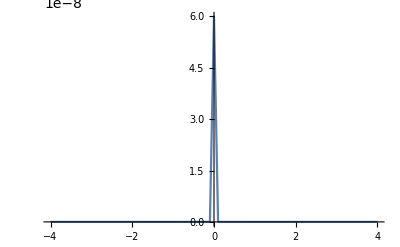

```mathematica
ListPlot[testvsw,PlotRange->All,Joined->True]
```

```mathematica
newspinsusw0qpipipartGS[kx_,ky_,μ_,t_,tp_,U_,β_]:=With[{tt=SortBy[Eigensystem[hamiltonian[kx,ky,μ,t,tp,U]//N]ᵀ,First]ᵀ,bar=256},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,1}];
-ParallelSum[(Exp[-β*tvals[[i]]]-Exp[-β*tvals[[j]]])/(tvals[[i]]-tvals[[j]]+0.00000001)/Z0*Abs[tvecs[[i]]†.spipi.tvecs[[j]]]^2,{i,bar},{j,bar}]/4];
newspinsusw0qpipiGS[nn_,t_,tp_,μ_,U_,β_]:=ParallelSum[newspinsusw0qpipipart[n1*Pi/nn+0.000001,n2*Pi/nn+0.000001,μ,t,tp,U,β],{n1,0,nn-1},{n2,0,nn-1}]/nn/nn;
```

```mathematica
testE=SortBy[Eigensystem[hamiltonian[Pi/10+0.00001,Pi/10+0.00001,4,1,0,8]//N]ᵀ,First]ᵀ;
```

```mathematica
testE[[1,1]]+16
```

-3.88963

```mathematica
newspinsusw0qpipipartGS[Pi/10+0.00001,Pi/10+0.00001,4,1,0,8,300]
```

6.92907

## equal-time spin correlation

```mathematica
newspinsust0q00part[kx_,ky_,μ_,t_,tp_,U_,β_]:=With[{tt=SortBy[Eigensystem[hamiltonian[kx,ky,μ,t,tp,U]//N]ᵀ,First]ᵀ,bar=256},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,bar}];
Sum[tvecs[[n]]†.s00.s00.tvecs[[n]]*(Exp[-β*tvals[[n]]]),{n,bar}]/Z0
];
newspinsust0q00[nn_,t_,tp_,μ_,U_,β_]:=ParallelSum[newspinsust0q00part[n1*Pi/nn+0.000001,n2*Pi/nn+0.000001,μ,t,tp,U,β],{n1,0,nn-1},{n2,0,nn-1}]/nn/nn/4;
newspinsust0qpipipart[kx_,ky_,μ_,t_,tp_,U_,β_]:=With[{tt=SortBy[Eigensystem[hamiltonian[kx,ky,μ,t,tp,U]//N]ᵀ,First]ᵀ,bar=16},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,bar}];
Sum[tvecs[[n]]†.spipi.spipi.tvecs[[n]]*(Exp[-β*tvals[[n]]]),{n,bar}]/Z0
];
newspinsust0qpipi[nn_,t_,tp_,μ_,U_,β_]:=ParallelSum[newspinsust0qpipipart[n1*Pi/nn+0.000001,n2*Pi/nn+0.000001,μ,t,tp,U,β],{n1,0,nn-1},{n2,0,nn-1}]/nn/nn/4;
```

```mathematica
U=6;mu=U/2;newspinsust0qpipipart[0/40*Pi+0.00001,0/40*Pi+0.00001,mu,1,0,U,10000]
```

0.5200391193

```mathematica
newspinsust0qpipipart[33/40*Pi+0.00001,11/40*Pi+0.00001,1,1,0,2,10000]
```

0.3704261598

```mathematica
newspinsust0qpipi[100,1,0,0,0,10000]
```

0.0621907

```mathematica
0.06219065432492177^0.5
```

0.249381

```mathematica
newspinsust0qpipi[100,1,0,0,0,10000]
```

```mathematica
nfilled[100,1,0,-0.2389,0,10000]
```

0.875056

```mathematica
newspinsust0qpipi[100,1,0,-0.2389,0,10000]
```

0.054691

```mathematica
0.05469100014759427^0.5
```

0.233861

```mathematica
nfilled[100,1,0,-0.4282,0,10000]
```

0.799965

```mathematica
newspinsust0qpipi[100,1,0,-0.4282,0,10000]
```

0.0499978

```mathematica
0.049997840669857026^0.5
```

0.223602

```mathematica
GSEpart[kx_,ky_,μ_,t_,tp_,U_,β_]:=With[{tt=SortBy[Eigensystem[hamiltonian[kx,ky,μ,t,tp,U]//N]ᵀ,First]ᵀ},
tt[[1,1]]+4*μ
];GSE[nn_,t_,tp_,μ_,U_,β_]:=ParallelSum[GSEpart[n1*Pi/nn,n2*Pi/nn,μ,t,tp,U,β],{n1,0,nn-1},{n2,0,nn-1}]/nn/nn/4;
```

```mathematica
GSE[40,1,0,-0.4282,0,10000]
```

```mathematica
GSE[100,1,0,-0.2389,0,10000]
```

-1.63763

```mathematica
GSE[100,1,0,-0.4282,0,10000]
```

-1.66871

```mathematica
U=0;mu=U/2;newspinsust0qpipi[100,1,0,mu,U,10000]
```

0.0621907

```mathematica
U=0;mu=U/2;newspinsust0qpipi[40,1,0,mu,U,10000]
```

0.0617384

```mathematica
U=2;mu=U/2;GSE[40,1,0,mu,U,10000]
```

-1.22676

```mathematica
U=2;mu=U/2;newspinsust0qpipi[100,1,0,mu,U,10000]
```

0.092979528919

```mathematica
0.09297952891940628948453761819237239905^0.5
```

0.304925

```mathematica
U=2;mu=U/2;newspinsust0qpipi[40,1,0,mu,U,10000]
```

0.092943066607

```mathematica
U=6;mu=U/2;newspinsust0qpipi[100,1,0,mu,U,10000]
```

0.1199950354

```mathematica
U=100;mu=U/2;newspinsust0qpipi[100,1,0,mu,U,10000]
```

0.146462569